```mathematica
<<CustomTicks`
```

```mathematica
(*yaxis1=yaxis2=LogTicks[-10,2];
Do[yaxis1[[i,1]]=10^(yaxis2[[i,1]]),{i,1,Length[yaxis1]}]
yaxis2[[1]]
xaxis10TeV={{200,200,{0.01,0},{}},{500,500,{0.01,0},{}},{1000,1000,{0.01,0},{}},{2000,2000,{0.01,0},{}},{5000,5000,{0.01,0},{}},{10000,"10^4",{0.01,0},{}},{300,"",{0.005,0},{}},{400,"",{0.005,0},{}},{600,"",{0.005,0},{}},{700,"",{0.005,0},{}},{800,"",{0.005,0},{}},{900,"",{0.005,0},{}},{3000,"",{0.005,0},{}},{4000,"",{0.005,0},{}},{6000,"",{0.005,0},{}},{7000,"",{0.005,0},{}},{8000,"",{0.005,0},{}},{9000,"",{0.005,0},{}}};*)
tickll=LogTicks[-8,0];
Do[tickll[[i,1]]=10^tickll[[i,1]],{i,1,Length[tickll]}];
tickll;
```

## Run2 result

#### input Run2 data

```mathematica
Signalrun2data=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\Run2\\lllv_signal_atlas_mlll_atlas.csv","CSV"];
lllvrun2data=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\Run2\\lllv_bkg_atlas_mlll_atlas.csv","CSV"];
llllrun2data=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\Run2\\llll_bkg_atlas_mlll_atlas.csv","CSV"];
ttrun2data=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\Run2\\tt_bkg_atlas_50_mlll_atlas.csv","CSV"];
```

#### input Run2 probability density data

```mathematica
Signalrun2data=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\Run2\\probability_density\\lllv_signal_atlas_mlll_atlas_density.csv","CSV"];
lllvrun2data=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\Run2\\probability_density\\lllv_bkg_atlas_mlll_atlas_density.csv","CSV"];
llllrun2data=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\Run2\\probability_density\\llll_bkg_atlas_mlll_atlas_density.csv","CSV"];
ttrun2data=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\Run2\\probability_density\\tt_bkg_atlas_50_mlll_atlas_density.csv","CSV"];
```

#### plot Run2 result

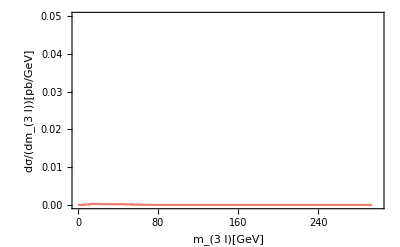

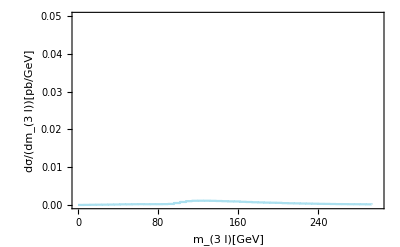

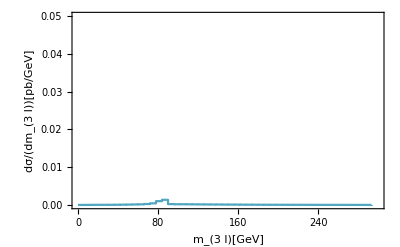

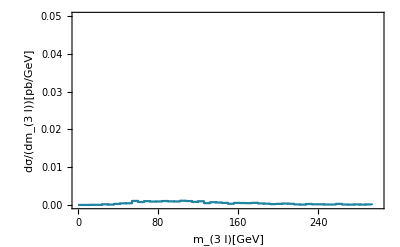

```mathematica
Signalrun2plot=ListPlot[Signalrun2data,Joined->True,InterpolationOrder->0,PlotRange->{{0,300},{0,0.05}},PlotStyle->{ColorData[24][1]},Frame->True,FrameLabel->{Style["m_(3  l)[GeV]",Black,13,FontFamily->"Times"],Style["dσ/(dm_(3  l))[pb/GeV]",Black,13,FontFamily->"Times"]}(*,FrameTicks->{{yaxis1,Automatic},{xaxis10TeV,Automatic}}*)]
lllvrun2plot=ListPlot[lllvrun2data,Joined->True,InterpolationOrder->0,PlotRange->{{0,300},{0,0.05}},PlotStyle->{ColorData[24][4]},Frame->True,FrameLabel->{Style["m_(3  l)[GeV]",Black,13,FontFamily->"Times"],Style["dσ/(dm_(3  l))[pb/GeV]",Black,13,FontFamily->"Times"]}]
llllrun2plot=ListPlot[llllrun2data,Joined->True,InterpolationOrder->0,PlotRange->{{0,300},{0,0.05}},PlotStyle->{ColorData[24][5]},Frame->True,FrameLabel->{Style["m_(3  l)[GeV]",Black,13,FontFamily->"Times"],Style["dσ/(dm_(3  l))[pb/GeV]",Black,13,FontFamily->"Times"]}]
ttrun2plot=ListPlot[ttrun2data,Joined->True,InterpolationOrder->0,PlotRange->{{0,300},{0,0.05}},PlotStyle->{ColorData[24][6]},Frame->True,FrameLabel->{Style["m_(3  l)[GeV]",Black,13,FontFamily->"Times"],Style["dσ/(dm_(3  l))[pb/GeV]",Black,13,FontFamily->"Times"]}]
```

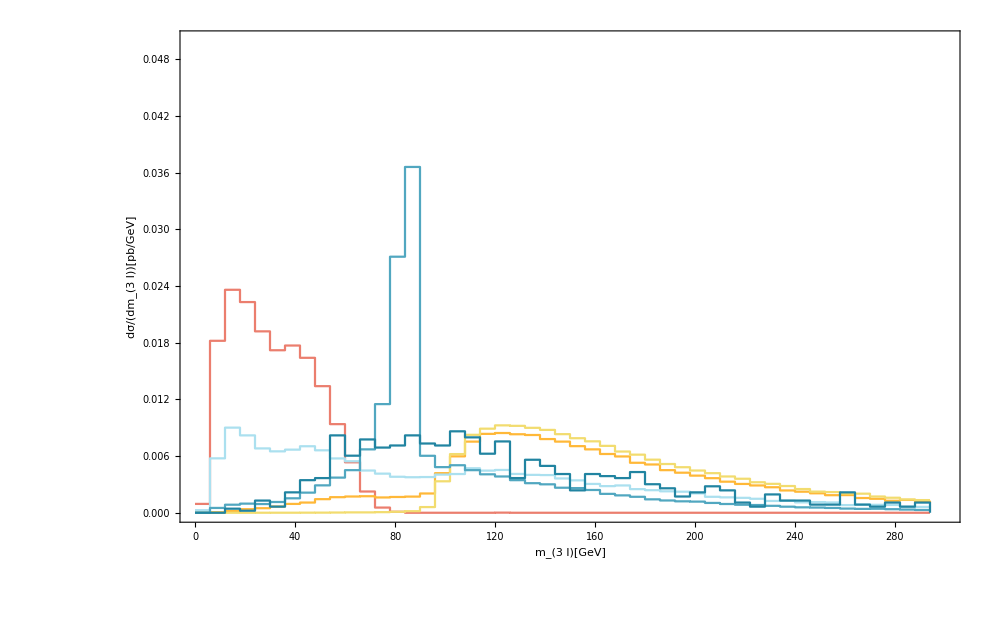

```mathematica
Run2Mlllplot=Show[Signalrun2plot,lllvrun2plot,llllrun2plot,ttrun2plot,FrameTicksStyle->Directive[Black,30,FontFamily->"Times"],PlotLegends->{Placed[LineLegend[{Style["[]",Black,13,FontFamily->"Times"],Style["[]",Black,13,FontFamily->"Times"],Style["[ -1/4]",Black,13,FontFamily->"Times"],Style["[-1/4, 0]",Black,13,FontFamily->"Times"],Style["[0, 1/4]",Black,13,FontFamily->"Times"],Style["[1/4, 1/2]",Black,13,FontFamily->"Times"]},LegendLayout->{"Row",2}],{{0.35,0.75},{0.25,0.3}}]},ImageSize->1000]
```

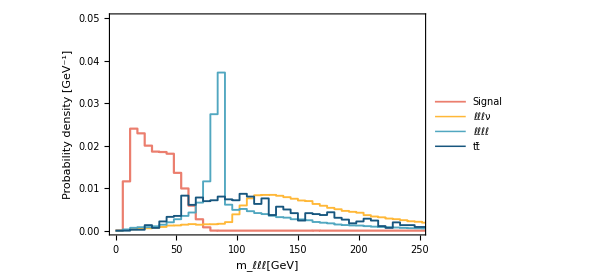

```mathematica
Run2Mlllplot=ListPlot[{Signalrun2data,lllvrun2data,llllrun2data,ttrun2data},Joined->True,PlotStyle->{Directive[ColorData[24][1],Thickness[0.0035]],Directive[ColorData[24][2],Thickness[0.003]],Directive[ColorData[24][5],Thickness[0.003]],Directive[ColorData[24][7],Thickness[0.003]]},PlotRange->{{0,250},{0,0.05}},InterpolationOrder->0,Frame->True,FrameLabel->{Style["m_ℓℓℓ[GeV]",Black,13,FontFamily->"Times"],Style["Probability density [GeV^-1]",Black,13,FontFamily->"Times"]},PlotLegends->{Placed[LineLegend[{Style["Signal",Black,13,FontFamily->"Times"],Style["ℓℓℓν",Black,13,FontFamily->"Times"],Style["ℓℓℓℓ",Black,13,FontFamily->"Times"],Style["tt̄",Black,13,FontFamily->"Times",Italic]},LegendLayout->{"Row",2}],{{0.35,0.80},{0.0,0.3}}]},FrameTicksStyle->Directive[Black,12,FontFamily->"Times"],ImageSize->450]
```

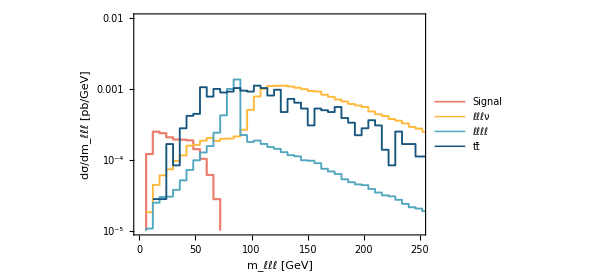

```mathematica
Run2Mlllplot=ListLogPlot[{Signalrun2data,lllvrun2data,llllrun2data,ttrun2data},Joined->True,PlotStyle->{Directive[ColorData[24][1],Thickness[0.0035]],Directive[ColorData[24][2],Thickness[0.003]],Directive[ColorData[24][5],Thickness[0.003]],Directive[ColorData[24][7],Thickness[0.003]]},PlotRange->{{0,250},{10^-5,0.01}},InterpolationOrder->0,Frame->True,FrameLabel->{Style["m_ℓℓℓ [GeV]",Black,13,FontFamily->"Times"],Style["dσ/dm_ℓℓℓ [pb/GeV]",Black,13,FontFamily->"Times"]},PlotLegends->{Placed[LineLegend[{Style["Signal",Black,13,FontFamily->"Times"],Style["ℓℓℓν",Black,13,FontFamily->"Times"],Style["ℓℓℓℓ",Black,13,FontFamily->"Times"],Style["tt̄",Black,13,FontFamily->"Times",Italic]},LegendLayout->{"Row",2}],{{0.35,0.80},{0.0,0.3}}]},FrameTicksStyle->Directive[Black,12,FontFamily->"Times"],ImageSize->450]
```

## HLLHC result

#### input HLLHC probability density data

```mathematica
bkghllhcdata=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\M_mumu\\HLLHC\\hist_all_hllhc_bkg_mll_v0.csv","CSV"];
(*lllvhllhcdata=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\HLLHC\\lllv_bkg_mlll.csv","CSV"];
llllhllhcdata=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\HLLHC\\llll_bkg_mlll.csv","CSV"];
tthllhcdata=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\HLLHC\\tt_bkg_50_mlll.csv","CSV"];*)

zp5hllhcdata=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\M_mumu\\HLLHC\\hist_all_hllhc_zp_5_mll.csv","CSV"];
zp20hllhcdata=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\M_mumu\\HLLHC\\hist_all_hllhc_zp_20_mll.csv","CSV"];
zp40hllhcdata=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\M_mumu\\HLLHC\\hist_all_hllhc_zp_40_mll.csv","CSV"];
zp60hllhcdata=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\M_mumu\\HLLHC\\hist_all_hllhc_zp_60_mll.csv","CSV"];
zp75hllhcdata=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\M_mumu\\HLLHC\\hist_all_hllhc_zp_75_mll.csv","CSV"];
```

#### plot HLLHC result

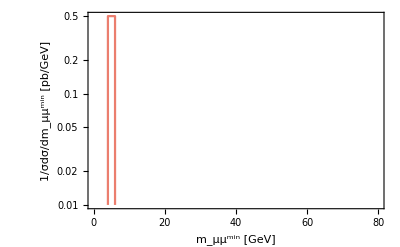

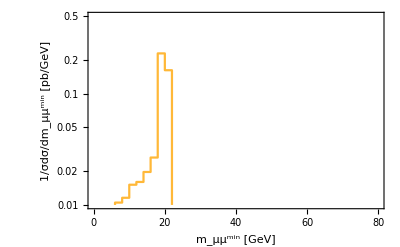

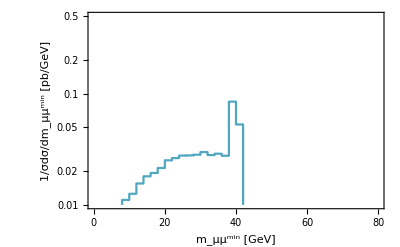

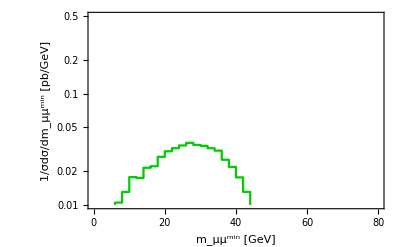

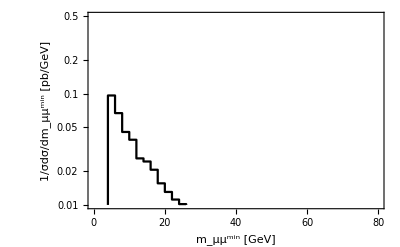

```mathematica
zp5hllhcplot=ListLogPlot[zp5hllhcdata,Joined->True,InterpolationOrder->0,PlotRange->{{0,80},{0.01,0.5}},PlotStyle->{ColorData[24][1]},Frame->True,FrameLabel->{Style["m_μμ^min [GeV]",Black,13,FontFamily->"Times"],Style["1/σdσ/dm_μμ^min [pb/GeV]",Black,13,FontFamily->"Times"]}(*,FrameTicks->{{yaxis1,Automatic},{xaxis10TeV,Automatic}}*)]
zp20hllhcplot=ListLogPlot[zp20hllhcdata,Joined->True,InterpolationOrder->0,PlotRange->{{0,80},{0.01,0.5}},PlotStyle->{ColorData[24][2]},Frame->True,FrameLabel->{Style["m_μμ^min [GeV]",Black,13,FontFamily->"Times"],Style["1/σdσ/dm_μμ^min [pb/GeV]",Black,13,FontFamily->"Times"]}]
zp40hllhcplot=ListLogPlot[zp40hllhcdata,Joined->True,InterpolationOrder->0,PlotRange->{{0,80},{0.01,0.5}},PlotStyle->{ColorData[24][5]},Frame->True,FrameLabel->{Style["m_μμ^min [GeV]",Black,13,FontFamily->"Times"],Style["1/σdσ/dm_μμ^min [pb/GeV]",Black,13,FontFamily->"Times"]}]
zp60hllhcplot=ListLogPlot[zp60hllhcdata,Joined->True,InterpolationOrder->0,PlotRange->{{0,80},{0.01,0.5}},PlotStyle->{Darker[Green,0.2]},Frame->True,FrameLabel->{Style["m_μμ^min [GeV]",Black,13,FontFamily->"Times"],Style["1/σdσ/dm_μμ^min [pb/GeV]",Black,13,FontFamily->"Times"]}]
(*zp75hllhcplot=ListPlot[zp75hllhcdata,Joined->True,InterpolationOrder->0,PlotRange->{{0,80},{0,0.05}},PlotStyle->{ColorData[24][8]},Frame->True,FrameLabel->{Style["m_μμ^min [GeV]",Black,13,FontFamily->"Times"],Style["1/σdσ/dm_μμ^min [pb/GeV]",Black,13,FontFamily->"Times"]}]*)
bkghllhcplot=ListLogPlot[bkghllhcdata,Joined->True,InterpolationOrder->0,PlotRange->{{0,80},{0.01,0.5}},PlotStyle->{Black},Frame->True,FrameLabel->{Style["m_μμ^min [GeV]",Black,13,FontFamily->"Times"],Style["1/σdσ/dm_μμ^min [pb/GeV]",Black,13,FontFamily->"Times"]}]
```

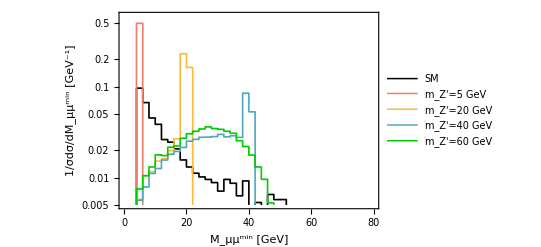

```mathematica
HLLHCMmumuplot=ListLogPlot[{bkghllhcdata,zp5hllhcdata,zp20hllhcdata,zp40hllhcdata,zp60hllhcdata},Joined->True,PlotStyle->{Directive[Black,Thickness[0.003]],Directive[ColorData[24][1],Thickness[0.003]],Directive[ColorData[24][2],Thickness[0.003]],Directive[ColorData[24][5],Thickness[0.003]],Directive[Darker[Green,0.2],Thickness[0.003]]},PlotRange->{{0,80},{0.005,0.6}},InterpolationOrder->0,Frame->True,FrameTicks->{{tickll,Automatic},{Automatic,Automatic}},FrameLabel->{Style[Row[{Subsuperscript[Style["M",FontSlant->"Plain"],Style["μμ"],Style["min"]]," [GeV]"}],Black,18,FontFamily->"Times"],Style["1/σdσ/dM_μμ^min [GeV^-1]",Black,17,FontFamily->"Times"]},PlotLegends->{Placed[LineLegend[{Style["SM",Black,14,FontFamily->"Times"],Style["m_Z'=5 GeV",Black,14,FontFamily->"Times"],Style["m_Z'=20 GeV",Black,14,FontFamily->"Times"],Style["m_Z'=40 GeV",Black,14,FontFamily->"Times"],Style["m_Z'=60 GeV",Black,14,FontFamily->"Times"]},LegendLayout->{"Column",1}],{{0.63,0.54},{0.0,0.3}}]},FrameTicksStyle->Directive[Black,14,FontFamily->"Times"],ImageSize->400]
```